```mathematica
filesAR=FileNames["/home/carla/GDC/SED/GDC_Conf_AR_SED_DOJ_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/SED/GDC_Conf_BR_SED_DOJ_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]]
confBR=dataBR[[All,1]]
```

{{0.00473934,1,211},{0.00473934,1,211},{0.00249377,1,401},{0.00051573,1,1939},{0.00054615,1,1831},{1.,1,1}}

{{0.00473934,101,21311},{0.00249377,16,6416},{0.00051573,70,135730},{0.00051573,1,1939},{0.00054615,1,1831}}

```mathematica
dojAR=confAR[[All,1]]
dojBR=confBR[[All,1]]
```

{0.00473934,0.00473934,0.00249377,0.00051573,0.00054615,1.}

{0.00473934,0.00249377,0.00051573,0.00051573,0.00054615}

```mathematica
sList={3,4,5,6,7,8};
sList2={3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];

dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&, ran2];
```

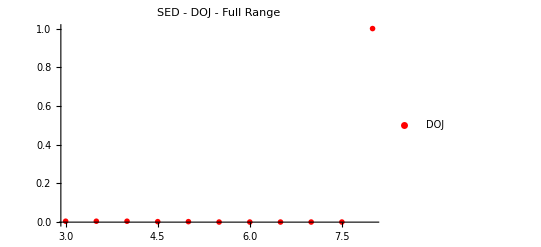

```mathematica
PlotDOJAllParts=ListPlot[{Union[dojPAR,dojPBR]}, PlotLegends->{"DOJ"}, PlotStyle-> {Red}, PlotRange->All, PlotLabel->"SED - DOJ - Full Range", PlotMarkers->{{"D",12}}]
```

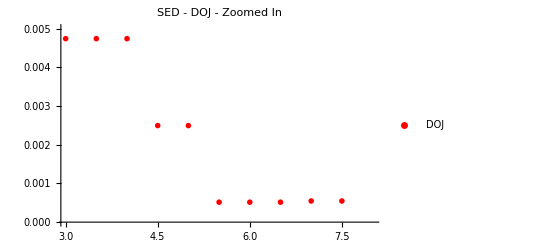

```mathematica
PlotDOJParts=ListPlot[{Union[dojPAR,dojPBR]}, PlotLegends->{"DOJ"}, PlotStyle-> {Red}, PlotRange->{0.0, 0.005},  PlotLabel->"SED - DOJ - Zoomed In",  PlotMarkers->{{"D",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/SED/"];
(*Put[{confM,{bvE,bvHEK}},filenameOut]*)
Put[Union[dojPAR,dojPBR],"SED_DOJ.txt"]
Export["SED_DOJ.jpeg",PlotDOJAllParts,ImageSize->850]
Export["SED_DOJ_Zoomed_In.jpeg",PlotDOJParts,ImageSize->850]
```

SED_DOJ.jpeg

SED_DOJ_Zoomed_In.jpeg

```mathematica
"SED_DOJ.jpeg"
```

SED_DOJ.jpeg

```mathematica
"SED_DOJ_Zoomed_In.jpeg"
```

SED_DOJ_Zoomed_In.jpeg